```mathematica
Remove["Global`*"];
Unprotect[In,Out];
Clear[In,Out];
Off[General::spell1]
```

```mathematica
data=ReadList["functf.dat",Number,RecordLists->True];
nOfFs=5;
radialCoord=ReadList["gridx.dat",Number];
angularCoord=ReadList["gridy.dat",Number];
nx=Length[radialCoord];
ny=Length[angularCoord];
```

```mathematica
dat=ArrayReshape[data,{nx ny,nOfFs}];
```

```mathematica
(* 1  2   3   4  5  6   7*)
(* nr,w,alpha,c1,c2,c3,rh*)
conf=ReadList["res.txt",{Number,Number ,Number ,Number ,Number,Number,Number }];

 
nr=conf[[1]][[1]];
rh= conf[[1]][[7]];
alfa= conf[[1]][[3]];
c1= conf[[1]][[4]];
c2= conf[[1]][[5]];
c3= conf[[1]][[6]]; 
w= conf[[1]][[2]];

Xtor[X_]:=If[X≠1,Sqrt[(X/(1-X))^2],1000]
f1=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,1]]},{i,1,ny},{j,1,nx}];
f2=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,2]]},{i,1,ny},{j,1,nx}];
f0=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,3]]},{i,1,ny},{j,1,nx}];
Z=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,4]]},{i,1,ny},{j,1,nx}];
W=Table[{radialCoord[[j]],angularCoord[[i]],dat[[j+(i-1)*nx,5]]},{i,1,ny},{j,1,nx}];
if1=Interpolation[Flatten[f1,1],InterpolationOrder->4];
if2=Interpolation[Flatten[f2,1],InterpolationOrder->4];
if0=Interpolation[Flatten[f0,1],InterpolationOrder->4];
iZ=Interpolation[Flatten[Z,1],InterpolationOrder->4];
iW=Interpolation[Flatten[W,1],InterpolationOrder->4];
f1=if1;
f2=if2;
f0=if0;
Z=iZ;
W=iW;
```

```mathematica
H[r_] := 1 - rh/r;
gtt[r_,θ_]:=-ⅇ^(2f0[r,θ]) H[r]+ⅇ^(2f2[r,θ]) r^2 W[r,θ]^2
rh
```

0.08

```mathematica
gttEq[r_] = gtt[r,π/2];
f1Eq[r_] = f1[r,π/2];
f2Eq[r_] = f2[r,π/2];
f0Eq[r_] = f0[r,π/2];
ZEq[r_] = Z[r,π/2];
WEq[r_] = W[r,π/2];
```

```mathematica
derVplus[r_]=WEq'[r]+(E^(f0Eq[r]-f2Eq[r]) (r H'[r]+2 H[r] (-1+r f0Eq'[r]-r f2Eq'[r])))/(2 r^2 Sqrt[H[r]]);
derVminus[r_] = WEq'[r]+(E^(f0Eq[r]-f2Eq[r]) (-r H'[r]+H[r] (2-2 r f0Eq'[r]+2 r f2Eq'[r])))/(2 r^2 Sqrt[H[r]]);
```

```mathematica
findRoots[f_,xMax_]:=Block[{zeros,soln,y,x},
reaping=Reap[soln=y[x]/.First[NDSolve[{y'[x]==Evaluate[D[f[x],x]],y[xMax]==(f[xMax])},y[x],{x,xMax,10^-16},Method->{"EventLocator","Event"->y[x],"EventAction":>Sow[{x,y[x]}]}]]][[2]];
zeros = If[Length[reaping]>0,reaping[[1]],{{xMax,0}}];
{Plot[f[x],{x,rh,xMax},Epilog->{PointSize[Medium],Red,Point[zeros]}],zeros[[All,1]]}]
findExtrema[f_,xMax_]:=Block[{zeros,soln,y,x},
reaping=Reap[soln=y[x]/.First[NDSolve[{y'[x]==Evaluate[D[f[x],x]],y[xMax]==(f[xMax])},y[x],{x,xMax,10^-16},Method->{"EventLocator","Event"->y'[x],"EventAction":>Sow[{x,y[x]}]}]]][[2]];
zeros = If[Length[reaping]>0,reaping[[1]],{{xMax,0}}];
{Plot[f[x],{x,rh,xMax},Epilog->{PointSize[Medium],Red,Point[zeros]}],zeros[[All,1]]}]
```

NDSolve::ndsz: At x == 0.08, step size is effectively zero; singularity or stiff system suspected.

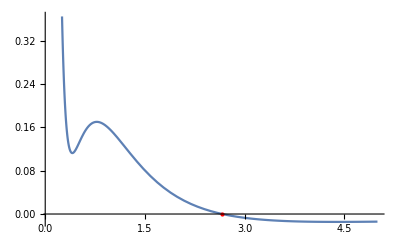
{-Graphics-,{2.66462}}

NDSolve::ndsz: At x == 0.08, step size is effectively zero; singularity or stiff system suspected.

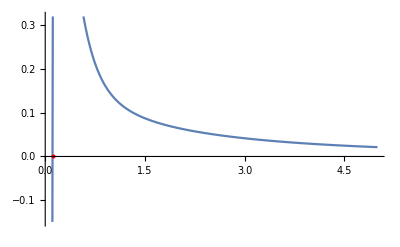
{-Graphics-,{0.109654}}

```mathematica
findRoots[derVplus,5]
findRoots[derVminus,5]
```